```mathematica
q=175
spinx[k_]:=Table[(KroneckerDelta[i,j+1]+KroneckerDelta[i+1,j])/2*Sqrt[k*(k+1)-i*j],{i,-k,k},{j,-k,k}]
spiny[k_]:=Table[(KroneckerDelta[i,j+1]-KroneckerDelta[i+1,j])/I/2*Sqrt[k*(k+1)-i*j],{i,-k,k},{j,-k,k}]
spinz[k_]:=Table[(KroneckerDelta[i,j])*i,{i,-k,k},{j,-k,k}]
```

175

{{{-Cos[θ],0,0,0,0,0},{0,-Cos[θ],0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,Cos[θ],0},{0,0,0,0,0,Cos[θ]}},{{0,0,(Cos[ϕ] Sin[θ])/(√2),0,0,0},{0,0,0,(Cos[ϕ] Sin[θ])/(√2),0,0},{(Cos[ϕ] Sin[θ])/(√2),0,0,0,(Cos[ϕ] Sin[θ])/(√2),0},{0,(Cos[ϕ] Sin[θ])/(√2),0,0,0,(Cos[ϕ] Sin[θ])/(√2)},{0,0,(Cos[ϕ] Sin[θ])/(√2),0,0,0},{0,0,0,(Cos[ϕ] Sin[θ])/(√2),0,0}},{{0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0},{0,0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0},{-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2),0},{0,-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2)},{0,0,-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0},{0,0,0,-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0}}}

{{{-Cos[θ]/2,0,0,0,0,0},{0,Cos[θ]/2,0,0,0,0},{0,0,-Cos[θ]/2,0,0,0},{0,0,0,Cos[θ]/2,0,0},{0,0,0,0,-Cos[θ]/2,0},{0,0,0,0,0,Cos[θ]/2}},{{0,1/2 Cos[ϕ] Sin[θ],0,0,0,0},{1/2 Cos[ϕ] Sin[θ],0,0,0,0,0},{0,0,0,1/2 Cos[ϕ] Sin[θ],0,0},{0,0,1/2 Cos[ϕ] Sin[θ],0,0,0},{0,0,0,0,0,1/2 Cos[ϕ] Sin[θ]},{0,0,0,0,1/2 Cos[ϕ] Sin[θ],0}},{{0,1/2 ⅈ Sin[θ] Sin[ϕ],0,0,0,0},{-1/2 ⅈ Sin[θ] Sin[ϕ],0,0,0,0,0},{0,0,0,1/2 ⅈ Sin[θ] Sin[ϕ],0,0},{0,0,-1/2 ⅈ Sin[θ] Sin[ϕ],0,0,0},{0,0,0,0,0,1/2 ⅈ Sin[θ] Sin[ϕ]},{0,0,0,0,-1/2 ⅈ Sin[θ] Sin[ϕ],0}}}

{{{-Cos[θ],0,0,0,0,0},{0,-Cos[θ],0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,Cos[θ],0},{0,0,0,0,0,Cos[θ]}},{{0,0,(Cos[ϕ] Sin[θ])/(√2),0,0,0},{0,0,0,(Cos[ϕ] Sin[θ])/(√2),0,0},{(Cos[ϕ] Sin[θ])/(√2),0,0,0,(Cos[ϕ] Sin[θ])/(√2),0},{0,(Cos[ϕ] Sin[θ])/(√2),0,0,0,(Cos[ϕ] Sin[θ])/(√2)},{0,0,(Cos[ϕ] Sin[θ])/(√2),0,0,0},{0,0,0,(Cos[ϕ] Sin[θ])/(√2),0,0}},{{0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0},{0,0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0},{-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2),0},{0,-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0,(ⅈ Sin[θ] Sin[ϕ])/(√2)},{0,0,-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0,0},{0,0,0,-(ⅈ Sin[θ] Sin[ϕ])/(√2),0,0}}}

{{{-Cos[θ]/2,0,0,0,0,0},{0,Cos[θ]/2,0,0,0,0},{0,0,-Cos[θ]/2,0,0,0},{0,0,0,Cos[θ]/2,0,0},{0,0,0,0,-Cos[θ]/2,0},{0,0,0,0,0,Cos[θ]/2}},{{0,1/2 Cos[ϕ] Sin[θ],0,0,0,0},{1/2 Cos[ϕ] Sin[θ],0,0,0,0,0},{0,0,0,1/2 Cos[ϕ] Sin[θ],0,0},{0,0,1/2 Cos[ϕ] Sin[θ],0,0,0},{0,0,0,0,0,1/2 Cos[ϕ] Sin[θ]},{0,0,0,0,1/2 Cos[ϕ] Sin[θ],0}},{{0,1/2 ⅈ Sin[θ] Sin[ϕ],0,0,0,0},{-1/2 ⅈ Sin[θ] Sin[ϕ],0,0,0,0,0},{0,0,0,1/2 ⅈ Sin[θ] Sin[ϕ],0,0},{0,0,-1/2 ⅈ Sin[θ] Sin[ϕ],0,0,0},{0,0,0,0,0,1/2 ⅈ Sin[θ] Sin[ϕ]},{0,0,0,0,-1/2 ⅈ Sin[θ] Sin[ϕ],0}}}

{{2870-4.2045 b,0.,0.,0.,0.,0.},{0.,2870-1.4015 b,0.,0.,0.,0.},{0.,0.,0.-1.4015 b,0.,0.,0.},{0.,0.,0.,0.+1.4015 b,0.,0.},{0.,0.,0.,0.,2870+1.4015 b,0.},{0.,0.,0.,0.,0.,2870+4.2045 b}}

{{1/2-(3 Cos[θ]^2)/2,0,0,-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),0,0},{0,-1/2+(3 Cos[θ]^2)/2,1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),0,0,0},{0,1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),0,0,0,-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2))},{-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),0,0,0,1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),0},{0,0,0,1/(√2)-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),-1/2+(3 Cos[θ]^2)/2,0},{0,0,-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)),0,0,1/2-(3 Cos[θ]^2)/2}}

{{0,1/2 Ω Cos[t ω],(Ω Cos[t ω])/(√2),0,0,0},{1/2 Ω Cos[t ω],0,0,(Ω Cos[t ω])/(√2),0,0},{(Ω Cos[t ω])/(√2),0,0,1/2 Ω Cos[t ω],(Ω Cos[t ω])/(√2),0},{0,(Ω Cos[t ω])/(√2),1/2 Ω Cos[t ω],0,0,(Ω Cos[t ω])/(√2)},{0,0,(Ω Cos[t ω])/(√2),0,0,1/2 Ω Cos[t ω]},{0,0,0,(Ω Cos[t ω])/(√2),1/2 Ω Cos[t ω],0}}

(5741/2-4.2045 b-(3 Cos[θ]^2)/2 | 0. | 0. | 0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0.
0. | 5739/2-1.4015 b+(3 Cos[θ]^2)/2 | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0. | 0.
0. | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0.-1.4015 b | 0. | 0. | 0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2))
0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0. | 0.+1.4015 b | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0.
0. | 0. | 0. | 0.707107-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)+(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 5739/2+1.4015 b+(3 Cos[θ]^2)/2 | 0.
0. | 0. | 0.-3 ((Cos[ϕ]^2 Sin[θ]^2)/(2 √2)-(Sin[θ]^2 Sin[ϕ]^2)/(2 √2)) | 0. | 0. | 5741/2+4.2045 b-(3 Cos[θ]^2)/2)

{{0,0,0},{√2,0,0},{0,√2,0}}

{{0,√2,0},{0,0,√2},{0,0,0}}

{{0,0},{1,0}}

{{0,1},{0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1/2,0,0,0},{0,0,0,1/2,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

2870

2.803

{{717.625,0.,0.,0.397748,0.,0.},{0.,2152.38,-0.0883883,0.,0.,0.},{0.,-0.0883883,-717.5,0.,0.,0.397748},{0.397748,0.,0.,717.5,-0.0883883,0.},{0.,0.,0.,-0.0883883,3587.38,0.},{0.,0.,0.397748,0.,0.,5022.63}}

(717.625 | 0. | 0. | 0.397748 | 0. | 0.
0. | 2152.38 | -0.0883883 | 0. | 0. | 0.
0. | -0.0883883 | -717.5 | 0. | 0. | 0.397748
0.397748 | 0. | 0. | 717.5 | -0.0883883 | 0.
0. | 0. | 0. | -0.0883883 | 3587.38 | 0.
0. | 0. | 0.397748 | 0. | 0. | 5022.63)

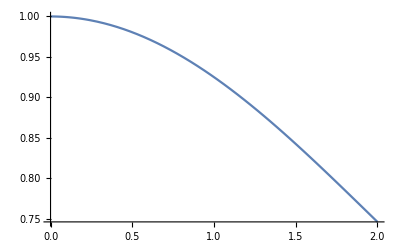

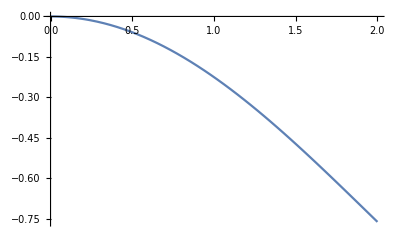

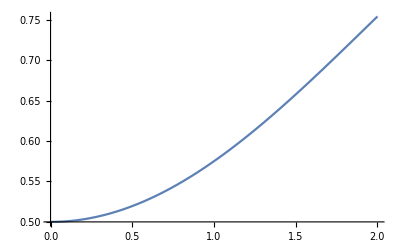

```mathematica
r={Cos[θ],Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ]};
tabnv={spinz[1],spinx[1],spiny[1]};
tabp1={spinz[1/2],spinx[1/2],spiny[1/2]};
tabnv=(KroneckerProduct[#,IdentityMatrix[2]]&)/@(r*tabnv)
tabp1=(KroneckerProduct[IdentityMatrix[3],(#)]&)/@(r*tabp1)
zeem=KroneckerProduct[spinz[1],IdentityMatrix[2]]*γ*b+KroneckerProduct[spinz[1].spinz[1],IdentityMatrix[2]]*d+γ*b*KroneckerProduct[IdentityMatrix[3],spinz[1/2]]
dipol=KroneckerProduct[spinx[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spinx[1/2]]+KroneckerProduct[spiny[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spiny[1/2]]+KroneckerProduct[spinz[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spinz[1/2]]-3*Total[MapThread[#1.#2&,{tabnv,tabp1}]]
mag=(KroneckerProduct[spinx[1],IdentityMatrix[2]]*Ω+KroneckerProduct[IdentityMatrix[3],spinx[1/2]]*Ω)*Cos[ω*t]
(hameff=zeem+dipol)//MatrixForm
nvp=spinx[1]+I*spiny[1]
nvm=spinx[1]-I*spiny[1]
p1p=spinx[1/2]+I*spiny[1/2]
p1m=spinx[1/2]-I*spiny[1/2]
ρ=KroneckerProduct[DiagonalMatrix[{0,1,0}],IdentityMatrix[2]]
ρ=ρ/Tr[ρ]
d=2870
γ=2.803
ham2=hameff/.θ->Pi/3/.ϕ->Pi/3/.b->d/γ/2
ham2//MatrixForm
rhosol=MatrixExp[-I*ham2*t].ρ.MatrixExp[I*ham2*t];
Plot[Tr[DiagonalMatrix[{0,0,1,1,0,0}].rhosol]/.d->2870,{t,0,2.001}]
Plot[Tr[spinz[5/2].rhosol//Chop],{t,0,2.001}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol],{t,0,2.001}]
```

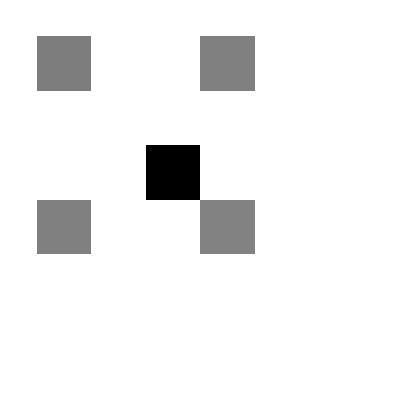

```mathematica
ArrayPlot[rhosol/.t->1]
```

```mathematica
hameff=hameff/.θ->Pi/3/.ϕ->Pi/3.
hameff+mag//MatrixForm
rotwav=MatrixExp[-I*hameff*t];
(rwaham=Refine[ConjugateTranspose[rotwav].(hameff+mag).rotwav-I*ConjugateTranspose[rotwav].D[rotwav,t]]);
```

{{22961/8-4.2045 b,0.,0.,0.397748,0.,0.},{0.,22959/8-1.4015 b,-0.0883883,0.,0.,0.},{0.,-0.0883883,0.-1.4015 b,0.,0.,0.397748},{0.397748,0.,0.,0.+1.4015 b,-0.0883883,0.},{0.,0.,0.,-0.0883883,22959/8+1.4015 b,0.},{0.,0.,0.397748,0.,0.,22961/8+4.2045 b}}

(22961/8-4.2045 b | 0.+1/2 Ω Cos[t ω] | 0.+(Ω Cos[t ω])/(√2) | 0.397748 | 0. | 0.
0.+1/2 Ω Cos[t ω] | 22959/8-1.4015 b | -0.0883883 | 0.+(Ω Cos[t ω])/(√2) | 0. | 0.
0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 0.-1.4015 b | 0.+1/2 Ω Cos[t ω] | 0.+(Ω Cos[t ω])/(√2) | 0.397748
0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+1/2 Ω Cos[t ω] | 0.+1.4015 b | -0.0883883 | 0.+(Ω Cos[t ω])/(√2)
0. | 0. | 0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 22959/8+1.4015 b | 0.+1/2 Ω Cos[t ω]
0. | 0. | 0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+1/2 Ω Cos[t ω] | 22961/8+4.2045 b)

```mathematica
rwaham
```

$Aborted[]

```mathematica
.. .
```

```mathematica
Diagonal[hameff]+717.568/.b->512//N
```

{1434.99,2869.88,0.,1435.14,4305.01,5740.4}

```mathematica
rotham=MatrixExp[-I*DiagonalMatrix[{1435,1435,0,1435,1435,1435}]*t]
```

{{ⅇ^(-1435 ⅈ t),0,0,0,0,0},{0,ⅇ^(-1435 ⅈ t),0,0,0,0},{0,0,1,0,0,0},{0,0,0,ⅇ^(-1435 ⅈ t),0,0},{0,0,0,0,ⅇ^(-1435 ⅈ t),0},{0,0,0,0,0,ⅇ^(-1435 ⅈ t)}}

```mathematica
rotwav=rotham
(rwaham=Refine[ConjugateTranspose[rotwav].(hameff+mag).rotwav-I*ConjugateTranspose[rotwav].D[rotwav,t]]);
```

{{ⅇ^(-1435 ⅈ t),0,0,0,0,0},{0,ⅇ^(-1435 ⅈ t),0,0,0,0},{0,0,1,0,0,0},{0,0,0,ⅇ^(-1435 ⅈ t),0,0},{0,0,0,0,ⅇ^(-1435 ⅈ t),0},{0,0,0,0,0,ⅇ^(-1435 ⅈ t)}}

{{ⅇ^((0.-1434.99 ⅈ) t),0,0,0,0,0},{0,ⅇ^((0.-2869.88 ⅈ) t),0,0,0,0},{0,0,1.+0. ⅈ,0,0,0},{0,0,0,ⅇ^((0.-1435.14 ⅈ) t),0,0},{0,0,0,0,ⅇ^((0.-4305.01 ⅈ) t),0},{0,0,0,0,0,ⅇ^((0.-5740.4 ⅈ) t)}}

{{ⅇ^((0.-1434.99 ⅈ) t),0,0,0,0,0},{0,ⅇ^((0.-2869.88 ⅈ) t),0,0,0,0},{0,0,1.+0. ⅈ,0,0,0},{0,0,0,ⅇ^((0.-1435.14 ⅈ) t),0,0},{0,0,0,0,ⅇ^((0.-4305.01 ⅈ) t),0},{0,0,0,0,0,ⅇ^((0.-5740.4 ⅈ) t)}}

(22961/8-4.2045 b | 0.+1/2 Ω Cos[t ω] | 0.+(Ω Cos[t ω])/(√2) | 0.397748 | 0. | 0.
0.+1/2 Ω Cos[t ω] | 22959/8-1.4015 b | -0.0883883 | 0.+(Ω Cos[t ω])/(√2) | 0. | 0.
0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 0.-1.4015 b | 0.+1/2 Ω Cos[t ω] | 0.+(Ω Cos[t ω])/(√2) | 0.397748
0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+1/2 Ω Cos[t ω] | 0.+1.4015 b | -0.0883883 | 0.+(Ω Cos[t ω])/(√2)
0. | 0. | 0.+(Ω Cos[t ω])/(√2) | -0.0883883 | 22959/8+1.4015 b | 0.+1/2 Ω Cos[t ω]
0. | 0. | 0.397748 | 0.+(Ω Cos[t ω])/(√2) | 0.+1/2 Ω Cos[t ω] | 22961/8+4.2045 b)

{{1435.13-4.2045 b,1/4 ⅇ^(-1435 ⅈ t) Ω+1/4 ⅇ^(1435 ⅈ t) Ω,Ω/(2 √2)+(ⅇ^(2870 ⅈ t) Ω)/(2 √2),0.397748,0,0},{1/4 ⅇ^(-1435 ⅈ t) Ω+1/4 ⅇ^(1435 ⅈ t) Ω,1434.88-1.4015 b,-0.0883883 ⅇ^(1435 ⅈ t),(ⅇ^(-1435 ⅈ t) Ω)/(2 √2)+(ⅇ^(1435 ⅈ t) Ω)/(2 √2),0,0},{Ω/(2 √2)+(ⅇ^(-2870 ⅈ t) Ω)/(2 √2),-0.0883883 ⅇ^(-1435 ⅈ t),-1.4015 b,Ω/4+1/4 ⅇ^(-2870 ⅈ t) Ω,Ω/(2 √2)+(ⅇ^(-2870 ⅈ t) Ω)/(2 √2),0.397748 ⅇ^(-1435 ⅈ t)},{0.397748,(ⅇ^(-1435 ⅈ t) Ω)/(2 √2)+(ⅇ^(1435 ⅈ t) Ω)/(2 √2),Ω/4+1/4 ⅇ^(2870 ⅈ t) Ω,-1435.+1.4015 b,-0.0883883,(ⅇ^(-1435 ⅈ t) Ω)/(2 √2)+(ⅇ^(1435 ⅈ t) Ω)/(2 √2)},{0,0,Ω/(2 √2)+(ⅇ^(2870 ⅈ t) Ω)/(2 √2),-0.0883883,1434.88+1.4015 b,1/4 ⅇ^(-1435 ⅈ t) Ω+1/4 ⅇ^(1435 ⅈ t) Ω},{0,0,0.397748 ⅇ^(1435 ⅈ t),(ⅇ^(-1435 ⅈ t) Ω)/(2 √2)+(ⅇ^(1435 ⅈ t) Ω)/(2 √2),1/4 ⅇ^(-1435 ⅈ t) Ω+1/4 ⅇ^(1435 ⅈ t) Ω,1435.13+4.2045 b}}

(1435.13-4.2045 b | 0 | Ω/(2 √2) | 0.397748 | 0 | 0
0 | 1434.88-1.4015 b | 0. | 0 | 0 | 0
Ω/(2 √2) | 0. | -1.4015 b | Ω/4 | Ω/(2 √2) | 0.
0.397748 | 0 | Ω/4 | -1435.+1.4015 b | -0.0883883 | 0
0 | 0 | Ω/(2 √2) | -0.0883883 | 1434.88+1.4015 b | 0
0 | 0 | 0. | 0 | 0 | 1435.13+4.2045 b)

{{-717.375,0,0,0.397748,0,0},{0,717.375,0.,0,0,0},{0,0.,-717.5,0,0,0.},{0.397748,0,0,-717.5,-0.0883883,0},{0,0,0,-0.0883883,2152.38,0},{0,0,0.,0,0,3587.63}}

-Graphics-

-Graphics-

{{-717.375,0,5/(2 √2),0.397748,0,0},{0,717.375,0.,0,0,0},{5/(2 √2),0.,-717.5,5/4,5/(2 √2),0.},{0.397748,0,5/4,-717.5,-0.0883883,0},{0,0,5/(2 √2),-0.0883883,2152.38,0},{0,0,0.,0,0,3587.63}}

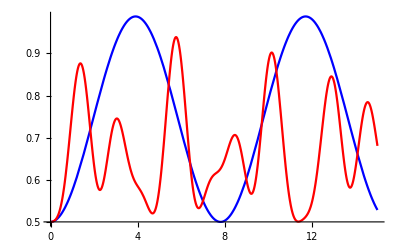

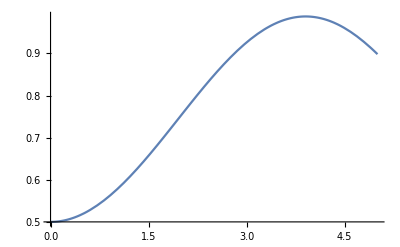

```mathematica
Diagonal[hameff]+717.568/.b->512//N;
rotham=MatrixExp[-I*DiagonalMatrix[Diagonal[hameff]+717.568/.b->512]*t]
rotwav=rotham
$Assumptions=Element[t,Reals];
hameff+mag//MatrixForm
rwaham=Refine[rwaham,Element[t,Reals]]/.ω->1435//Simplify//TrigToExp//Simplify//Expand//Chop
(rwaham2=Map[If[FreeQ[#,t],#,0]&,rwaham//Expand,{3}])//MatrixForm
rwaham3=rwaham2/.b->d/γ/2/.Ω->0
rhosol1=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t]//Chop;
Plot[Tr[DiagonalMatrix[{0,0,1,1,0,0}].rhosol]/.d->2870,{t,0,2.001}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol],{t,0,2.001}]
rwaham3=rwaham2/.b->d/γ/2/.Ω->5
rhosol2=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t]//Chop;
dat=Chop[(Tr[DiagonalMatrix[{1,0,1,0,1,0}].#]&)]/@{Chop@rhosol1,Chop@rhosol2};
Plot[dat,{t,0,15.001},PlotStyle->{Blue,Red}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol]//Chop,{t,0,5.001}]
```

```mathematica
rotham=MatrixExp[-I*DiagonalMatrix[{478,0,0,478,478,478}]*t]
rotwav=rotham
$Assumptions=Element[t,Reals];
hameff+mag//N//MatrixForm
rwaham=Refine[rwaham,Element[t,Reals]]/.ω->478.//Simplify//TrigToExp//Simplify//Expand//Chop
rwaham//Simplify//MatrixForm
(rwaham2=Map[If[FreeQ[#,t],#,0]&,rwaham//Expand,{3}])//MatrixForm
rwaham3=rwaham2/.b->d/γ/3/.Ω->0
rwaham3//MatrixForm
```

{{ⅇ^(-478 ⅈ t),0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,ⅇ^(-478 ⅈ t),0,0},{0,0,0,0,ⅇ^(-478 ⅈ t),0},{0,0,0,0,0,ⅇ^(-478 ⅈ t)}}

{{ⅇ^(-478 ⅈ t),0,0,0,0,0},{0,1,0,0,0,0},{0,0,1,0,0,0},{0,0,0,ⅇ^(-478 ⅈ t),0,0},{0,0,0,0,ⅇ^(-478 ⅈ t),0},{0,0,0,0,0,ⅇ^(-478 ⅈ t)}}

(2870.13-4.2045 b | 0.+0.5 Ω Cos[t ω] | 0.+0.707107 Ω Cos[t ω] | 0.397748 | 0. | 0.
0.+0.5 Ω Cos[t ω] | 2869.88-1.4015 b | -0.0883883 | 0.+0.707107 Ω Cos[t ω] | 0. | 0.
0.+0.707107 Ω Cos[t ω] | -0.0883883 | 0.-1.4015 b | 0.+0.5 Ω Cos[t ω] | 0.+0.707107 Ω Cos[t ω] | 0.397748
0.397748 | 0.+0.707107 Ω Cos[t ω] | 0.+0.5 Ω Cos[t ω] | 0.+1.4015 b | -0.0883883 | 0.+0.707107 Ω Cos[t ω]
0. | 0. | 0.+0.707107 Ω Cos[t ω] | -0.0883883 | 2869.88+1.4015 b | 0.+0.5 Ω Cos[t ω]
0. | 0. | 0.397748 | 0.+0.707107 Ω Cos[t ω] | 0.+0.5 Ω Cos[t ω] | 2870.13+4.2045 b)

{{1435.13-4.2045 b,1/4 ⅇ^((0.-1435. ⅈ) t) Ω+1/4 ⅇ^((0.+1435. ⅈ) t) Ω,0.353553 Ω+0.353553 ⅇ^((0.+2870. ⅈ) t) Ω,0.397748,0,0},{1/4 ⅇ^((0.-1435. ⅈ) t) Ω+1/4 ⅇ^((0.+1435. ⅈ) t) Ω,1434.88-1.4015 b,-0.0883883 ⅇ^(1435 ⅈ t),(ⅇ^((0.-1435. ⅈ) t) Ω)/(2 √2)+(ⅇ^((0.+1435. ⅈ) t) Ω)/(2 √2),0,0},{0.353553 Ω+0.353553 ⅇ^((0.-2870. ⅈ) t) Ω,-0.0883883 ⅇ^(-1435 ⅈ t),-1.4015 b,0.25 Ω+1/4 ⅇ^((0.-2870. ⅈ) t) Ω,0.353553 Ω+0.353553 ⅇ^((0.-2870. ⅈ) t) Ω,0.397748 ⅇ^(-1435 ⅈ t)},{0.397748,(ⅇ^((0.-1435. ⅈ) t) Ω)/(2 √2)+(ⅇ^((0.+1435. ⅈ) t) Ω)/(2 √2),0.25 Ω+0.25 ⅇ^((0.+2870. ⅈ) t) Ω,-1435.+1.4015 b,-0.0883883,(ⅇ^((0.-1435. ⅈ) t) Ω)/(2 √2)+(ⅇ^((0.+1435. ⅈ) t) Ω)/(2 √2)},{0,0,0.353553 Ω+0.353553 ⅇ^((0.+2870. ⅈ) t) Ω,-0.0883883,1434.88+1.4015 b,1/4 ⅇ^((0.-1435. ⅈ) t) Ω+1/4 ⅇ^((0.+1435. ⅈ) t) Ω},{0,0,0.397748 ⅇ^(1435 ⅈ t),(ⅇ^((0.-1435. ⅈ) t) Ω)/(2 √2)+(ⅇ^((0.+1435. ⅈ) t) Ω)/(2 √2),1/4 ⅇ^((0.-1435. ⅈ) t) Ω+1/4 ⅇ^((0.+1435. ⅈ) t) Ω,1435.13+4.2045 b}}

(1435.13-4.2045 b | 1/4 ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω | (0.353553+0.353553 ⅇ^((0.+2870. ⅈ) t)) Ω | 0.397748 | 0 | 0
1/4 ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω | 1434.88-1.4015 b | -0.0883883 ⅇ^(1435 ⅈ t) | (ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω)/(2 √2) | 0 | 0
(0.353553+0.353553 ⅇ^((0.-2870. ⅈ) t)) Ω | -0.0883883 ⅇ^(-1435 ⅈ t) | -1.4015 b | 1/4 (1.+ⅇ^((0.-2870. ⅈ) t)) Ω | (0.353553+0.353553 ⅇ^((0.-2870. ⅈ) t)) Ω | 0.397748 ⅇ^(-1435 ⅈ t)
0.397748 | (ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω)/(2 √2) | (0.25+0.25 ⅇ^((0.+2870. ⅈ) t)) Ω | -1435.+1.4015 b | -0.0883883 | (ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω)/(2 √2)
0 | 0 | (0.353553+0.353553 ⅇ^((0.+2870. ⅈ) t)) Ω | -0.0883883 | 1434.88+1.4015 b | 1/4 ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω
0 | 0 | 0.397748 ⅇ^(1435 ⅈ t) | (ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω)/(2 √2) | 1/4 ⅇ^((0.-1435. ⅈ) t) (1+ⅇ^((0.+2870. ⅈ) t)) Ω | 1435.13+4.2045 b)

(1435.13-4.2045 b | 0 | 0.353553 Ω | 0.397748 | 0 | 0
0 | 1434.88-1.4015 b | 0. | 0 | 0 | 0
0.353553 Ω | 0. | -1.4015 b | 0.25 Ω | 0.353553 Ω | 0.
0.397748 | 0 | 0.25 Ω | -1435.+1.4015 b | -0.0883883 | 0
0 | 0 | 0.353553 Ω | -0.0883883 | 1434.88+1.4015 b | 0
0 | 0 | 0. | 0 | 0 | 1435.13+4.2045 b)

{{0.125,0,0.,0.397748,0,0},{0,956.542,0.,0,0,0},{0.,0.,-478.333,0.,0.,0.},{0.397748,0,0.,-956.667,-0.0883883,0},{0,0,0.,-0.0883883,1913.21,0},{0,0,0.,0,0,2870.13}}

(0.125 | 0 | 0. | 0.397748 | 0 | 0
0 | 956.542 | 0. | 0 | 0 | 0
0. | 0. | -478.333 | 0. | 0. | 0.
0.397748 | 0 | 0. | -956.667 | -0.0883883 | 0
0 | 0 | 0. | -0.0883883 | 1913.21 | 0
0 | 0 | 0. | 0 | 0 | 2870.13)

```mathematica
r={Cos[θ],Sin[θ]*Cos[ϕ],Sin[θ]*Sin[ϕ]};
tabnv={spinz[1],spinx[1],spiny[1]};
tabp1={spinz[1/2],spinx[1/2],spiny[1/2]};
tabnv=(KroneckerProduct[#,IdentityMatrix[2]]&)/@(r*tabnv)
tabp1=(KroneckerProduct[IdentityMatrix[3],(#)]&)/@(r*tabp1)
zeem=KroneckerProduct[spinz[1],IdentityMatrix[2]]*γ*b+KroneckerProduct[spinz[1].spinz[1],IdentityMatrix[2]]*d+γ*b*KroneckerProduct[IdentityMatrix[3],spinz[1/2]]
dipol=KroneckerProduct[spinx[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spinx[1/2]]+KroneckerProduct[spiny[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spiny[1/2]]+KroneckerProduct[spinz[1],IdentityMatrix[2]].KroneckerProduct[IdentityMatrix[3],spinz[1/2]]-3*Total[MapThread[#1.#2&,{tabnv,tabp1}]]
mag=(KroneckerProduct[spinx[1],IdentityMatrix[2]]*Ω2*Cos[ω2*t]+KroneckerProduct[IdentityMatrix[3],spinx[1/2]]*Ω1*Cos[ω1*t])
(hameff=zeem+dipol)//MatrixForm
nvp=spinx[1]+I*spiny[1]
nvm=spinx[1]-I*spiny[1]
p1p=spinx[1/2]+I*spiny[1/2]
p1m=spinx[1/2]-I*spiny[1/2]
ρ=KroneckerProduct[DiagonalMatrix[{0,1,0}],IdentityMatrix[2]]
ρ=ρ/Tr[ρ]
d=2870
γ=2.803
ham2=hameff/.θ->Pi/3/.ϕ->Pi/3/.b->d/γ/2
ham2//MatrixForm
```

{{{-1/2,0,0,0,0,0},{0,-1/2,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,0,0,1/2,0},{0,0,0,0,0,1/2}},{{0,0,(√(3/2))/4,0,0,0},{0,0,0,(√(3/2))/4,0,0},{(√(3/2))/4,0,0,0,(√(3/2))/4,0},{0,(√(3/2))/4,0,0,0,(√(3/2))/4},{0,0,(√(3/2))/4,0,0,0},{0,0,0,(√(3/2))/4,0,0}},{{0,0,(3 ⅈ)/(4 √2),0,0,0},{0,0,0,(3 ⅈ)/(4 √2),0,0},{-(3 ⅈ)/(4 √2),0,0,0,(3 ⅈ)/(4 √2),0},{0,-(3 ⅈ)/(4 √2),0,0,0,(3 ⅈ)/(4 √2)},{0,0,-(3 ⅈ)/(4 √2),0,0,0},{0,0,0,-(3 ⅈ)/(4 √2),0,0}}}

{{{-1/4,0,0,0,0,0},{0,1/4,0,0,0,0},{0,0,-1/4,0,0,0},{0,0,0,1/4,0,0},{0,0,0,0,-1/4,0},{0,0,0,0,0,1/4}},{{0,(√3)/8,0,0,0,0},{(√3)/8,0,0,0,0,0},{0,0,0,(√3)/8,0,0},{0,0,(√3)/8,0,0,0},{0,0,0,0,0,(√3)/8},{0,0,0,0,(√3)/8,0}},{{0,(3 ⅈ)/8,0,0,0,0},{-(3 ⅈ)/8,0,0,0,0,0},{0,0,0,(3 ⅈ)/8,0,0},{0,0,-(3 ⅈ)/8,0,0,0},{0,0,0,0,0,(3 ⅈ)/8},{0,0,0,0,-(3 ⅈ)/8,0}}}

{{2870-4.2045 b,0.,0.,0.,0.,0.},{0.,2870-1.4015 b,0.,0.,0.,0.},{0.,0.,0.-1.4015 b,0.,0.,0.},{0.,0.,0.,0.+1.4015 b,0.,0.},{0.,0.,0.,0.,2870+1.4015 b,0.},{0.,0.,0.,0.,0.,2870+4.2045 b}}

{{1/8,0,0,9/(16 √2),0,0},{0,-1/8,-1/(8 √2),0,0,0},{0,-1/(8 √2),0,0,0,9/(16 √2)},{9/(16 √2),0,0,0,-1/(8 √2),0},{0,0,0,-1/(8 √2),-1/8,0},{0,0,9/(16 √2),0,0,1/8}}

{{0,1/2 Ω1 Cos[1154.84 t],(Ω2 Cos[1715.29 t])/(√2),0,0,0},{1/2 Ω1 Cos[1154.84 t],0,0,(Ω2 Cos[1715.29 t])/(√2),0,0},{(Ω2 Cos[1715.29 t])/(√2),0,0,1/2 Ω1 Cos[1154.84 t],(Ω2 Cos[1715.29 t])/(√2),0},{0,(Ω2 Cos[1715.29 t])/(√2),1/2 Ω1 Cos[1154.84 t],0,0,(Ω2 Cos[1715.29 t])/(√2)},{0,0,(Ω2 Cos[1715.29 t])/(√2),0,0,1/2 Ω1 Cos[1154.84 t]},{0,0,0,(Ω2 Cos[1715.29 t])/(√2),1/2 Ω1 Cos[1154.84 t],0}}

(22961/8-4.2045 b | 0. | 0. | 0.397748 | 0. | 0.
0. | 22959/8-1.4015 b | -0.0883883 | 0. | 0. | 0.
0. | -0.0883883 | 0.-1.4015 b | 0. | 0. | 0.397748
0.397748 | 0. | 0. | 0.+1.4015 b | -0.0883883 | 0.
0. | 0. | 0. | -0.0883883 | 22959/8+1.4015 b | 0.
0. | 0. | 0.397748 | 0. | 0. | 22961/8+4.2045 b)

{{0,0,0},{√2,0,0},{0,√2,0}}

{{0,√2,0},{0,0,√2},{0,0,0}}

{{0,0},{1,0}}

{{0,1},{0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1,0,0,0},{0,0,0,1,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

{{0,0,0,0,0,0},{0,0,0,0,0,0},{0,0,1/2,0,0,0},{0,0,0,1/2,0,0},{0,0,0,0,0,0},{0,0,0,0,0,0}}

2870

2.803

{{717.625,0.,0.,0.397748,0.,0.},{0.,2152.38,-0.0883883,0.,0.,0.},{0.,-0.0883883,-717.5,0.,0.,0.397748},{0.397748,0.,0.,717.5,-0.0883883,0.},{0.,0.,0.,-0.0883883,3587.38,0.},{0.,0.,0.397748,0.,0.,5022.63}}

(717.625 | 0. | 0. | 0.397748 | 0. | 0.
0. | 2152.38 | -0.0883883 | 0. | 0. | 0.
0. | -0.0883883 | -717.5 | 0. | 0. | 0.397748
0.397748 | 0. | 0. | 717.5 | -0.0883883 | 0.
0. | 0. | 0. | -0.0883883 | 3587.38 | 0.
0. | 0. | 0.397748 | 0. | 0. | 5022.63)

```mathematica
Clear[Ω1]
Clear[Ω2]
```

```mathematica
hameff
```

{{22961/8-4.2045 b,0.,0.,0.397748,0.,0.},{0.,22959/8-1.4015 b,-0.0883883,0.,0.,0.},{0.,-0.0883883,0.-1.4015 b,0.,0.,0.397748},{0.397748,0.,0.,0.+1.4015 b,-0.0883883,0.},{0.,0.,0.,-0.0883883,22959/8+1.4015 b,0.},{0.,0.,0.397748,0.,0.,22961/8+4.2045 b}}

```mathematica
Diagonal[hameff]/.b->412//N
rotham=MatrixExp[-I*DiagonalMatrix[Diagonal[hameff]/.b->412]*t];
rotwav=rotham;
θ=Pi/3
ϕ=Pi/3
```

{1137.87,2292.46,-577.418,577.418,3447.29,4602.38}

π/3

π/3

```mathematica
ω1=1137.87+577.418
ω2=2*577.418
Ω1=1
Ω2=1
```

1715.29

1154.84

1

1

```mathematica
Diagonal[hameff]/.b->412//N
rotham=MatrixExp[-I*DiagonalMatrix[Diagonal[hameff]/.b->412]*t]
hameff/.b->412//MatrixForm
ω2=-(#[[3]]-#[[1]])&@Diagonal[hameff]/.b->412
ω1=(#[[4]]-#[[3]])&@Diagonal[hameff]/.b->412
```

{1137.87,2292.46,-577.418,577.418,3447.29,4602.38}

{{ⅇ^((0.-1137.87 ⅈ) t),0,0,0,0,0},{0,ⅇ^((0.-2292.46 ⅈ) t),0,0,0,0},{0,0,ⅇ^((0.+577.418 ⅈ) t),0,0,0},{0,0,0,ⅇ^((0.-577.418 ⅈ) t),0,0},{0,0,0,0,ⅇ^((0.-3447.29 ⅈ) t),0},{0,0,0,0,0,ⅇ^((0.-4602.38 ⅈ) t)}}

(1137.87 | 0. | 0. | 0.397748 | 0. | 0.
0. | 2292.46 | -0.0883883 | 0. | 0. | 0.
0. | -0.0883883 | -577.418 | 0. | 0. | 0.397748
0.397748 | 0. | 0. | 577.418 | -0.0883883 | 0.
0. | 0. | 0. | -0.0883883 | 3447.29 | 0.
0. | 0. | 0.397748 | 0. | 0. | 4602.38)

1715.29

1154.84

(22961/8-4.2045 b | 0.+1/2 Ω1 Cos[1154.84 t] | 0.+(Ω2 Cos[1715.29 t])/(√2) | 0.397748 | 0. | 0.
0.+1/2 Ω1 Cos[1154.84 t] | 22959/8-1.4015 b | -0.0883883 | 0.+(Ω2 Cos[1715.29 t])/(√2) | 0. | 0.
0.+(Ω2 Cos[1715.29 t])/(√2) | -0.0883883 | 0.-1.4015 b | 0.+1/2 Ω1 Cos[1154.84 t] | 0.+(Ω2 Cos[1715.29 t])/(√2) | 0.397748
0.397748 | 0.+(Ω2 Cos[1715.29 t])/(√2) | 0.+1/2 Ω1 Cos[1154.84 t] | 0.+1.4015 b | -0.0883883 | 0.+(Ω2 Cos[1715.29 t])/(√2)
0. | 0. | 0.+(Ω2 Cos[1715.29 t])/(√2) | -0.0883883 | 22959/8+1.4015 b | 0.+1/2 Ω1 Cos[1154.84 t]
0. | 0. | 0.397748 | 0.+(Ω2 Cos[1715.29 t])/(√2) | 0.+1/2 Ω1 Cos[1154.84 t] | 22961/8+4.2045 b)

{{1732.25-4.2045 b,1/4 ⅇ^((0.+0.25 ⅈ) t) Ω1+1/4 ⅇ^((0.-2309.42 ⅈ) t) Ω1,0.353553 Ω2+0.353553 ⅇ^((0.+3430.58 ⅈ) t) Ω2,0.397748 ⅇ^((0.+560.453 ⅈ) t),0,0},{1/4 ⅇ^((0.-0.25 ⅈ) t) Ω1+1/4 ⅇ^((0.+2309.42 ⅈ) t) Ω1,577.418-1.4015 b,-0.0883883 ⅇ^((0.+2869.88 ⅈ) t),(ⅇ^((0.-0.25 ⅈ) t) Ω2)/(2 √2)+(ⅇ^((0.+3430.33 ⅈ) t) Ω2)/(2 √2),0,0},{0.353553 Ω2+0.353553 ⅇ^((0.-3430.58 ⅈ) t) Ω2,-0.0883883 ⅇ^((0.-2869.88 ⅈ) t),577.418-1.4015 b,0.25 Ω1+1/4 ⅇ^((0.-2309.67 ⅈ) t) Ω1,(ⅇ^((0.-2309.42 ⅈ) t) Ω2)/(2 √2)+(ⅇ^((0.-5740. ⅈ) t) Ω2)/(2 √2),0.397748 ⅇ^((0.-5179.8 ⅈ) t)},{0.397748 ⅇ^((0.-560.453 ⅈ) t),(ⅇ^((0.+0.25 ⅈ) t) Ω2)/(2 √2)+(ⅇ^((0.-3430.33 ⅈ) t) Ω2)/(2 √2),0.25 Ω1+0.25 ⅇ^((0.+2309.67 ⅈ) t) Ω1,-577.418+1.4015 b,-0.0883883 ⅇ^((0.-2869.88 ⅈ) t),(ⅇ^((0.-2309.67 ⅈ) t) Ω2)/(2 √2)+(ⅇ^((0.-5740.25 ⅈ) t) Ω2)/(2 √2)},{0,0,(ⅇ^((0.+2309.42 ⅈ) t) Ω2)/(2 √2)+(ⅇ^((0.+5740. ⅈ) t) Ω2)/(2 √2),-0.0883883 ⅇ^((0.+2869.88 ⅈ) t),-577.418+1.4015 b,1/4 ⅇ^((0.-0.25 ⅈ) t) Ω1+1/4 ⅇ^((0.-2309.92 ⅈ) t) Ω1},{0,0,0.397748 ⅇ^((0.+5179.8 ⅈ) t),(ⅇ^((0.+2309.67 ⅈ) t) Ω2)/(2 √2)+(ⅇ^((0.+5740.25 ⅈ) t) Ω2)/(2 √2),1/4 ⅇ^((0.+0.25 ⅈ) t) Ω1+1/4 ⅇ^((0.+2309.92 ⅈ) t) Ω1,-1732.25+4.2045 b}}

(1732.25-4.2045 b | 0 | 0.353553 Ω2 | 0. | 0 | 0
0 | 577.418-1.4015 b | 0. | 0 | 0 | 0
0.353553 Ω2 | 0. | 577.418-1.4015 b | 0.25 Ω1 | 0 | 0.
0. | 0 | 0.25 Ω1 | -577.418+1.4015 b | 0. | 0
0 | 0 | 0 | 0. | -577.418+1.4015 b | 0
0 | 0 | 0. | 0 | 0 | -1732.25+4.2045 b)

{{-420.246,0,0.,0.,0,0},{0,-140.082,0.,0,0,0},{0.,0.,-140.082,0.,0,0.},{0.,0,0.,140.082,0.,0},{0,0,0,0.,140.082,0},{0,0,0.,0,0,420.246}}

{{-420.246,0,1.76777,0.,0,0},{0,-140.082,0.,0,0,0},{1.76777,0.,-140.082,1.76777,0,0.},{0.,0,1.76777,140.082,0.,0},{0,0,0,0.,140.082,0},{0,0,0.,0,0,420.246}}

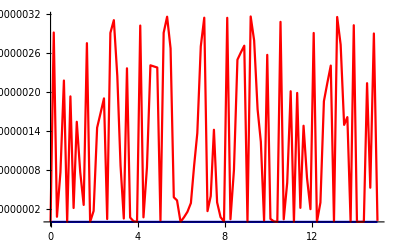

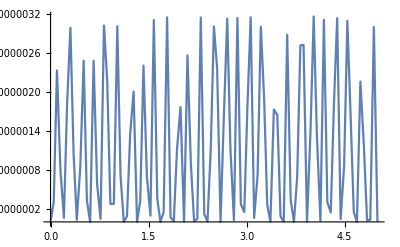

```mathematica
(rwaham=Refine[ConjugateTranspose[rotwav].(hameff+mag).rotwav-I*ConjugateTranspose[rotwav].D[rotwav,t]]);
$Assumptions=Element[t,Reals];
hameff+mag//MatrixForm
rwaham=Refine[rwaham,Element[t,Reals]]//Simplify//TrigToExp//Simplify//Expand//Chop
(rwaham2=Map[If[FreeQ[#,t],#,0]&,rwaham//Expand,{3}])//MatrixForm
rwaham3=rwaham2/.b->d/γ/2/.Ω1->0/.Ω2->0
rhosol1=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t];
rwaham3=rwaham2/.b->d/γ/2/.Ω1->5*Sqrt[2]/.Ω2->5
rhosol2=MatrixExp[-I*rwaham3*t].ρ.MatrixExp[I*rwaham3*t];
dat=(Tr[DiagonalMatrix[{1,0,1,0,1,0}].#]&)/@{rhosol1,rhosol2};
Plot[dat,{t,0,15.001},PlotStyle->{Blue,Red}]
Plot[Tr[DiagonalMatrix[{1,0,1,0,1,0}].rhosol2],{t,0,5.001}]
```

```mathematica
rwaham3//MatrixForm
```

(-420.246 | 0 | 1.76777 | 0. | 0 | 0
0 | -140.082 | 0. | 0 | 0 | 0
1.76777 | 0. | -140.082 | 1.76777 | 0 | 0.
0. | 0 | 1.76777 | 140.082 | 0. | 0
0 | 0 | 0 | 0. | 140.082 | 0
0 | 0 | 0. | 0 | 0 | 420.246)

```mathematica
577/2.803*2
```

411.702

```mathematica
d
```

2870

```mathematica
γ
```

2.803

```mathematica
d/γ/2
```

511.951

```mathematica
rwaham2/.b->d/γ/2//MatrixForm
```

(-420.246 | 0 | 0.353553 Ω2 | 0. | 0 | 0
0 | -140.082 | 0. | 0 | 0 | 0
0.353553 Ω2 | 0. | -140.082 | 0.25 Ω1 | 0 | 0.
0. | 0 | 0.25 Ω1 | 140.082 | 0. | 0
0 | 0 | 0 | 0. | 140.082 | 0
0 | 0 | 0. | 0 | 0 | 420.246)